```mathematica
EntityValue[EntityClass["Country",{EntityProperty["Country","BoundaryLength"]->TakeLargest[10]}],EntityProperty["Country","BoundaryLength"],"EntityAssociation"]
```

Get me the 5 largest companies by revenue

```mathematica
EntityValue[
  EntityClass["Company",{EntityProperty["Company","Revenue"]->TakeLargest[5]}],
  {"Name","Revenue"},
  "EntityAssociation"
]
```

Show me all the properties for the company entity

```mathematica
EntityProperties["Company"]
```

Use those to get me the 5 largest companies by revenue

```mathematica
EntityValue[
    EntityClass["Company",{EntityProperty["Company","TotalRevenue"]->TakeLargest[5]}],
    {"Name","TotalRevenue"},
    "EntityAssociation"
]
```

Get me a bar chart of those

```mathematica
data=EntityValue[
    EntityClass["Company",{EntityProperty["Company","TotalRevenue"]->TakeLargest[20]}],
    {"Name","TotalRevenue"}
];
```

```mathematica
BarChart[
    data[[All,2]],
    ChartLabels->Placed[data[[All,1]],"End"],
    BarOrigin->Left,
    ChartStyle->"Pastel",
    Frame->True,
    FrameLabel->{"Revenue (USD)",None},
    PlotLabel->"Top 5 Companies by Revenue"
]
```

Which companies are which color?

```mathematica
BarChart[
    data[[All,2]],
    ChartLabels->Placed[data[[All,1]],"End"],
    BarOrigin->Left,
    ChartStyle->"Pastel",
    Frame->True,
    FrameLabel->{"Revenue (USD)",None},
    PlotLabel->"Top 5 Companies by Revenue",
    ChartLegends->Placed[data[[All,1]],"Top"]
]
```

Do the same thing by profit

```mathematica
dataProfit=EntityValue[
	    EntityClass["Company",{EntityProperty["Company","NetIncome"]->TakeLargest[50]}],
	    {"Name","NetIncome"}
	];

BarChart[
	    dataProfit[[All,2]],
	    ChartLabels->Placed[dataProfit[[All,1]],"End"],
	    BarOrigin->Left,
	    ChartStyle->"Pastel",
	    Frame->True,
	    FrameLabel->{"Profit (USD)",None},
	    PlotLabel->"Top 5 Companies by Profit",
	    ChartLegends->Placed[dataProfit[[All,1]],"Top"]
	]
```

Show me the dataset on apple

```mathematica
Entity["Company","Apple::5zkjq"]
```

Now get  me the dataset on it

```mathematica
Entity["Company","Apple::5zkjq"]["Dataset"]
```

Get me the city of apple

```mathematica
EntityValue[Entity["Company","Apple::5zkjq"],"City"]
```

Show me where that city is on a map U.S. map

```mathematica
GeoGraphics[
    GeoMarker[Entity["City",{"Cupertino","California","UnitedStates"}]],
    GeoRange->"Country",
    PlotLabel->"Location of Cupertino, California"
]
```

Get me the cities of the top 5 companies by profit

```mathematica
dataProfit=EntityValue[
		    EntityClass["Company",{EntityProperty["Company","NetIncome"]->TakeLargest[5]}],
		    {"Name","City"}
		];
dataProfit
```

Now map those

```mathematica
GeoGraphics[
	    GeoMarker/@dataProfit[[All,2]],
	    GeoRange->"World",
	    PlotLabel->"Top 5 Companies by Profit - City Locations"
	]
```

Now do the top 20 companies

```mathematica
dataProfitTop20=EntityValue[
			    EntityClass["Company",{EntityProperty["Company","NetIncome"]->TakeLargest[20]}],
			    {"Name","City"}
			];
	
GeoGraphics[
		    GeoMarker/@dataProfitTop20[[All,2]],
		    GeoRange->"World",
		    PlotLabel->"Top 20 Companies by Profit - City Locations"
		]
```

Top 50?

```mathematica
dataProfitTop50=EntityValue[
				    EntityClass["Company",{EntityProperty["Company","NetIncome"]->TakeLargest[50]}],
				    {"Name","City"}
				];
		
	GeoGraphics[
			    GeoMarker/@dataProfitTop50[[All,2]],
			    GeoRange->"World",
			    PlotLabel->"Top 50 Companies by Profit - City Locations"
			]
```

```mathematica
top50 = EntityValue[
    EntityClass["Company",{EntityProperty["Company","TotalRevenue"]->TakeLargest[50]}],
    {"NetIncome", "City"}, "EntityAssociation"
]
```

from the above top50 list get me the companies that are in the U.S.

```mathematica
usCompaniesTop50=Select[top50,#[[2,2]][[2]]==="UnitedStates"&];
usCompaniesTop50
```

find what country the first company in top50 is in

```mathematica
byCountry = #["Country"]&/@ top50[[All, 2]]
```

```mathematica
Union[Values@byCountry]
```

```mathematica
us = Select[byCountry, # == Entity["Country","UnitedStates"]&]
```

```mathematica
totalProfitUS=Total@DeleteMissing[EntityValue[#,"NetIncome"]&/@ Keys@us] ;
totalProfitUS
```

now do the same for china and europe

```mathematica
countries ={ Entity["Country","Canada"],Entity["Country","China"],Entity["Country","France"],Entity["Country","Germany"],Entity["Country","Italy"],Entity["Country","Japan"],Entity["Country","Netherlands"],Entity["Country","Russia"],Entity["Country","SouthKorea"],Entity["Country","Switzerland"],Entity["Country","Taiwan"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"]}
```

do it for all of the above countries

```mathematica
getTotalProfit[country_]:=
```

Complete the definition of the above function

```mathematica
getTotalProfit[country_]:=Total@DeleteMissing[
    EntityValue[#,"NetIncome"]&/@
    Keys@Select[byCountry,#==country&]
]

(* Example usage *)
getTotalProfit[Entity["Country","UnitedStates"]]
```

Run that on all the countries

```mathematica
totalProfits=Association[
    #->getTotalProfit[#]&/@countries
];

totalProfits
```

Barchart

```mathematica
BarChart[
	    Values[totalProfits],
	    ChartLabels->Placed[Keys[totalProfits],"Below"],
	    PlotLabel->"Total Profits by Country",
	    BarOrigin->Left,
	    ImageSize->Large,
	    LabelStyle->{FontSize->12}
	]
```

Label with country name

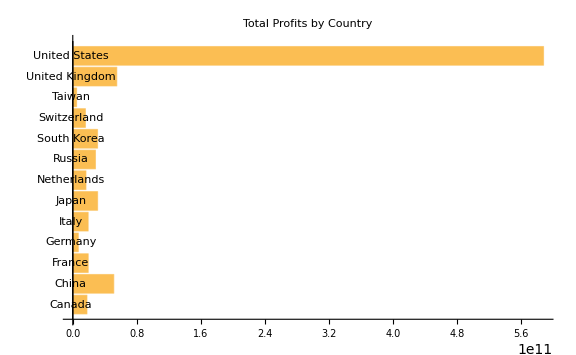

```mathematica
BarChart[
		    Values[totalProfits],
ChartLabels->countryNames,
		    PlotLabel->"Total Profits by Country",
		    BarOrigin->Left,
		    ImageSize->Large,
		    LabelStyle->{FontSize->12}
		]
```

get the names of all the countries as strings

```mathematica
countryNames=EntityValue[countries,"Name"]
```

```mathematica
Table[BarChart[SeedRandom[1];RandomReal[1,{4,5}],ChartLayout->l],{l,{"Stacked","Percentile"}}]
```

```mathematica
SeedRandom[1];RandomReal[1,{4,5}]
```

```mathematica
fromCountry[country_]:= Select[byCountry, # == country&]
```

```mathematica
comsTable = fromCountry/@ countries
```

{<|Cash Store Financial→Canada|>,<|China Petroleum→China,PetroChina Co→China,China Railway Group→China,Ping An Insurance (Group)→China,JD.com→China|>,<|TotalEnergies→France|>,<|Uniper→Germany,Volkswagen→Germany,Allianz→Germany,Mercedes-Benz Group AG→Germany|>,<|Enel→Italy,Eni→Italy|>,<|Toyota Motor→Japan,Mitsubishi→Japan|>,<|Stellantis→Netherlands|>,<|Gazprom→Russia|>,<|Samsung Electronics Co→South Korea|>,<|Glencore→Switzerland|>,<|Hon Hai Precision→Taiwan|>,<|Shell→United Kingdom,BP→United Kingdom|>,<|Walmart→United States,Amazon.com→United States,Apple→United States,UnitedHealth Group→United States,Berkshire Hathaway→United States,CVS Health→United States,Exxon Mobil→United States,Alphabet→United States,McKesson→United States,CoreSite Realty→United States,AmerisourceBergen→United States,Costco Wholesale→United States,Microsoft→United States,Cardinal Health→United States,Chevron→United States,Cigna→United States,Ford Motor→United States,General Motors→United States,Anthem→United States,JPMorgan Chase→United States,Home Depot→United States,Marathon Petroleum→United States,Valero Energy→United States,Centene→United States,Phillips 66→United States,Kroger→United States,Walgreens Boots Alliance→United States,Cargill→United States|>}

get the profit for each company for each country in a list of lists

```mathematica
companyProfitsByCountry=Table[
    DeleteMissing[
        EntityValue[Keys[fromCountry[country]],"NetIncome"]
    ],
    {country,countries}
];
companyProfitsByCountry
```

{{1.77087×10^10 $},{9.85311×10^9 $,1.99023×10^10 $,4.19025×10^9 $,1.39794×10^10 $,3.28163×10^9 $},{19286000000 $},{-3.96619×10^10 $,1.62375×10^10 $,7.06382×10^9 $,2.32611×10^10 $},{4.60184×10^9 $,1.46123×10^10 $},{2.16869×10^10 $,9.31171×10^9 $},{1.64751×10^10 $},{2.83182×10^10 $},{3.09431×10^10 $},{15782000000 $},{4.77368×10^9 $},{29297000000 $,25670000000 $},{16292000000 $,20079000000 $,96995000000 $,21687000000 $,76813000000 $,8600000000 $,41130000000 $,66732000000 $,3488000000 $,1746000000 $,1616848000 $,6292000000 $,77096000000 $,156000000 $,25463000000 $,5304000000 $,6162000000 $,9931000000 $,6080000000 $,49486000000 $,15704000000 $,11542000000 $,10710000000 $,2444000000 $,7629000000 $,1862000000 $,-3080000000 $}}

Barchart those with each company being stacked. Each country should be a separate bar

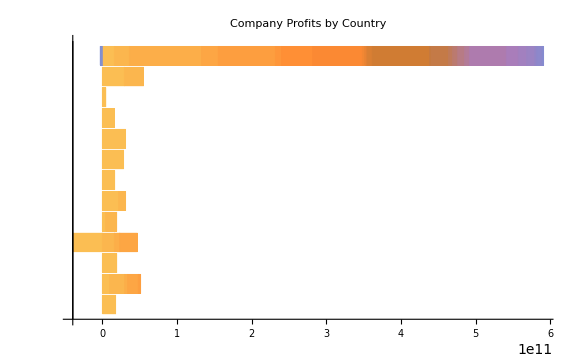

```mathematica
BarChart[
    companyProfitsByCountry,
    ChartLabels->Tooltip[companyNamesByCountry],
    ChartLayout->"Stacked",
    PlotLabel->"Company Profits by Country",
    BarOrigin->Left,
    ImageSize->Large,
    LabelStyle->{FontSize->12}
]
```

get all the company names in that same list of list format

```mathematica
companyNamesByCountry=Table[
	    EntityValue[Keys[fromCountry[country]],"Name"],
	    {country,countries}
	];
companyNamesByCountry
```

{{Cash Store Financial},{China Petroleum,PetroChina Co,China Railway Group,Ping An Insurance (Group),JD.com},{TotalEnergies},{Uniper,Volkswagen,Allianz,Mercedes-Benz Group AG},{Enel,Eni},{Toyota Motor,Mitsubishi},{Stellantis},{Gazprom},{Samsung Electronics Co},{Glencore},{Hon Hai Precision},{Shell,BP},{Walmart,Amazon.com,Apple,UnitedHealth Group,Berkshire Hathaway,CVS Health,Exxon Mobil,Alphabet,McKesson,CoreSite Realty,AmerisourceBergen,Costco Wholesale,Microsoft,Cardinal Health,Chevron,Cigna,Ford Motor,General Motors,Anthem,JPMorgan Chase,Home Depot,Marathon Petroleum,Valero Energy,Centene,Phillips 66,Kroger,Walgreens Boots Alliance,Cargill}}

now barchart that list

```mathematica
BarChart[
	    companyProfitsTooltip,
	    ChartLabels->Placed[countryNames,"Below"],
	    ChartLayout->"Stacked",
	    PlotLabel->"Company Profits by Country",
	    BarOrigin->Left,
	    ImageSize->Large,
	    LabelStyle->{FontSize->12}
	]
```

-Graphics-

Do the same bar chart as above but label each bar with the country on the y-axis

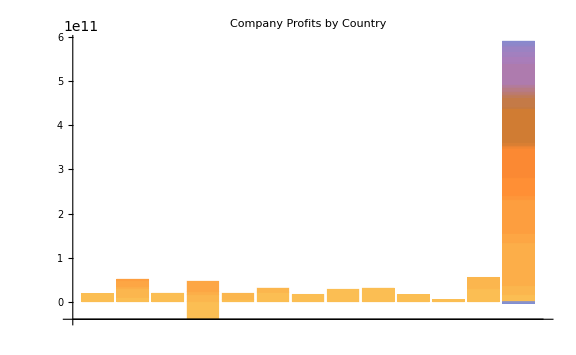

```mathematica
BarChart[
		    companyProfitsTooltip,
		    ChartLabels->Placed[countryNames,"Left"],
		    ChartLayout->"Stacked",
		    PlotLabel->"Company Profits by Country",
		    BarOrigin->Bottom,
		    ImageSize->Large,
		    LabelStyle->{FontSize->12}
		]
```

Use map thread to create a tooltip for each company

```mathematica
companyProfitsTooltip
```

{{1.77087×10^10 $},{9.85311×10^9 $,1.99023×10^10 $,4.19025×10^9 $,1.39794×10^10 $,3.28163×10^9 $},{19286000000 $},{-3.96619×10^10 $,1.62375×10^10 $,7.06382×10^9 $,2.32611×10^10 $},{4.60184×10^9 $,1.46123×10^10 $},{2.16869×10^10 $,9.31171×10^9 $},{1.64751×10^10 $},{2.83182×10^10 $},{3.09431×10^10 $},{15782000000 $},{4.77368×10^9 $},{29297000000 $,25670000000 $},{16292000000 $,20079000000 $,96995000000 $,21687000000 $,76813000000 $,8600000000 $,41130000000 $,66732000000 $,3488000000 $,1746000000 $,1616848000 $,6292000000 $,77096000000 $,156000000 $,25463000000 $,5304000000 $,6162000000 $,9931000000 $,6080000000 $,49486000000 $,15704000000 $,11542000000 $,10710000000 $,2444000000 $,7629000000 $,1862000000 $,-3080000000 $}}

```mathematica
Length/@ companyProfitsByCountry
```

{1,5,1,4,2,2,1,1,1,1,1,2,27}

```mathematica
Length/@ companyNamesByCountry
```

{1,5,1,4,2,2,1,1,1,1,1,2,27}

```mathematica
companyNamesByCountry = Delete[companyNamesByCountry, {-1, -1}]
```

{{Cash Store Financial},{China Petroleum,PetroChina Co,China Railway Group,Ping An Insurance (Group),JD.com},{TotalEnergies},{Uniper,Volkswagen,Allianz,Mercedes-Benz Group AG},{Enel,Eni},{Toyota Motor,Mitsubishi},{Stellantis},{Gazprom},{Samsung Electronics Co},{Glencore},{Hon Hai Precision},{Shell,BP},{Walmart,Amazon.com,Apple,UnitedHealth Group,Berkshire Hathaway,CVS Health,Exxon Mobil,Alphabet,McKesson,CoreSite Realty,AmerisourceBergen,Costco Wholesale,Microsoft,Cardinal Health,Chevron,Cigna,Ford Motor,General Motors,Anthem,JPMorgan Chase,Home Depot,Marathon Petroleum,Valero Energy,Centene,Phillips 66,Kroger,Walgreens Boots Alliance}}

```mathematica
companyProfitsTooltip=MapThread[
    Tooltip[#1,#2]&,
    {companyProfitsByCountry,companyNamesByCountry},
    2
];
```

MapThread::mptd: Object … at position {2, 1} in … has only 1 of required 2 dimensions.

```mathematica
getToolTip[country_, name_]:= Tooltip[country,name]
```

Complete the above functi

Do an example mapthread on a 2d array

```mathematica
example2DArray1={{1,2,3},{4,5,6},{7,8,9, 10}};
example2DArray2={{"a","b","c"},{"d","e","f"},{"g","h","i", "j"}};

result=MapThread[Tooltip[#1,#2]&,{example2DArray1,example2DArray2},2];
result
```

MapThread::mptd: Object {{1,2,3},{4,5,6},{7,8,9,10}} at position {2, 1} in MapThread[#1&,{{{1,2,3},{4,5,6},{7,8,9,10}},{{a,b,c},{d,e,f},{g,h,i,j}}},2] has only 1 of required 2 dimensions.

MapThread[#1&,{{{1,2,3},{4,5,6},{7,8,9,10}},{{a,b,c},{d,e,f},{g,h,i,j}}},2]

alternative way to do this other than mapthread

```mathematica
result=MapIndexed[
    Tooltip[#1,example2DArray2[[#2[[1]],#2[[2]]]]]&,
    example2DArray1,
    {2}
];
result
```

{{1,2,3},{4,5,6},{7,8,9,10}}

Do it for the real data now

```mathematica
companyProfitsTooltip=MapIndexed[
	    Tooltip[#1,companyNamesByCountry[[#2[[1]],#2[[2]]]]]&,
	    companyProfitsByCountry,
	    {2}
	];
```

```mathematica
Entity["Company","Apple::5zkjq"]
```

Apple

Get me apple's total employees

```mathematica
Entity["Company","WalMartStores::zsp93"]["Employees"]
```

2100000 people

Get me a barchart of the top50 companies and there employee number

```mathematica
top50 // Keys
```

{Walmart,Amazon.com,China Petroleum,PetroChina Co,Apple,UnitedHealth Group,Berkshire Hathaway,CVS Health,Exxon Mobil,Shell,Uniper,Alphabet,McKesson,Toyota Motor,Volkswagen,CoreSite Realty,AmerisourceBergen,Glencore,Costco Wholesale,Cash Store Financial,TotalEnergies,Samsung Electronics Co,BP,Microsoft,Hon Hai Precision,Cardinal Health,Chevron,Enel,Cigna,Eni,Stellantis,Ford Motor,General Motors,Anthem,China Railway Group,Ping An Insurance (Group),Allianz,JPMorgan Chase,Home Depot,Marathon Petroleum,Valero Energy,Centene,Phillips 66,JD.com,Mercedes-Benz Group AG,Kroger,Mitsubishi,Walgreens Boots Alliance,Gazprom,Cargill}

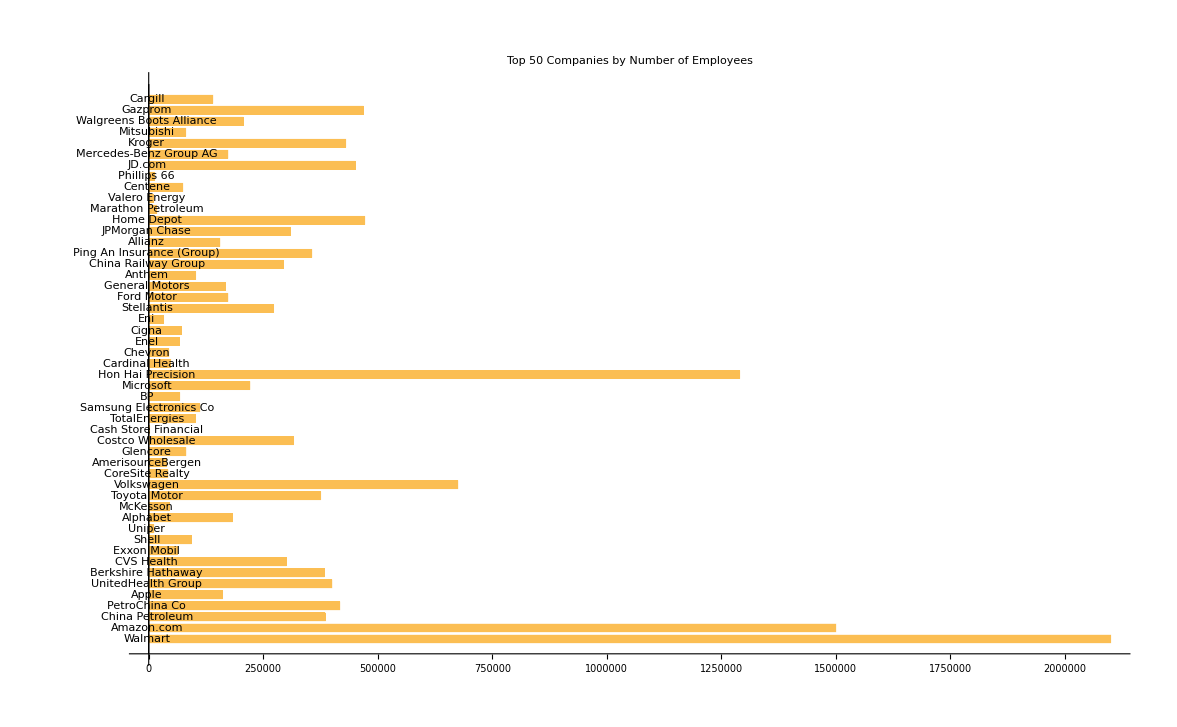

```mathematica
employeeCounts=EntityValue[Keys[top50],"Employees"];
BarChart[
    employeeCounts,
    ChartLabels->top50Names,
    PlotLabel->"Top 50 Companies by Number of Employees",
    BarOrigin->Left,
    ImageSize->Large,
    LabelStyle->{FontSize->12}
]
```

```mathematica
top50Names = #["Name"]&/@Keys[top50]
```

{Walmart,Amazon.com,China Petroleum,PetroChina Co,Apple,UnitedHealth Group,Berkshire Hathaway,CVS Health,Exxon Mobil,Shell,Uniper,Alphabet,McKesson,Toyota Motor,Volkswagen,CoreSite Realty,AmerisourceBergen,Glencore,Costco Wholesale,Cash Store Financial,TotalEnergies,Samsung Electronics Co,BP,Microsoft,Hon Hai Precision,Cardinal Health,Chevron,Enel,Cigna,Eni,Stellantis,Ford Motor,General Motors,Anthem,China Railway Group,Ping An Insurance (Group),Allianz,JPMorgan Chase,Home Depot,Marathon Petroleum,Valero Energy,Centene,Phillips 66,JD.com,Mercedes-Benz Group AG,Kroger,Mitsubishi,Walgreens Boots Alliance,Gazprom,Cargill}

## Military conflicts

Get me a random military conflict

```mathematica
RandomEntity["MilitaryConflict"]
```

```mathematica
Entity["MilitaryConflict","BattleOfTricamarum"]["MilitaryCasualties"] // DeleteMissing // Total
```

3000 people

```mathematica
EntityProperty["MilitaryConflict","MilitaryCasualties"] // InputForm
```

EntityProperty["MilitaryConflict", "MilitaryCasualties"]

```mathematica
{Missing["NotAvailable"],Quantity[3000, "People"]}
```

Get the largest military conflicts by military forces

```mathematica
EntityValue[
  EntityClass["MilitaryConflict",{EntityProperty["MilitaryConflict","ForcesMilitaryForces"]->TakeLargest[5]}],
  {"AllActors","ForcesMilitaryForces"},
  "EntityAssociation"
]
```

Missing[QueryValueIncompatibleWithProperty,{MilitaryConflict,ForcesMilitaryForces,TakeLargest[5]}]

```mathematica
largestConflicts=EntityClass["MilitaryConflict","LargestByForces"];
	conflictNames=EntityValue[largestConflicts,"Name"];
	conflictForces=EntityValue[largestConflicts,"ForcesMilitaryForces"];
	
	conflictWithMaxForces=Map[Max,conflictForces];
	SortedLargestConflicts=SortBy[Thread[{conflictNames,conflictWithMaxForces}],Last,Greater];
	SortedLargestConflicts
```

{Missing[UnknownEntityClass,{MilitaryConflict,LargestByForces}],Missing[UnknownEntityClass,Max[LargestByForces,MilitaryConflict]]}

```mathematica
recentConflictsClass = EntityClass["MilitaryConflict", 
{"StartDate" -> 
   Between[{DateObject[{1900}], DateObject[{1902}]}]}]
```

EntityClass[MilitaryConflict,{StartDate→Between[{Year: 1900,Year: 1902}]}]

Show me the "ForcesMilitartyForces" of all of recent conflicts class

the min and unit part doesn't work. You need to use a different method to access those. Also get rid of the echos

```mathematica
totalForces[forceList_]:=
				        If[MatchQ[forceList,_List],
				            Module[{forces=DeleteMissing@forceList},
				                Total[forces/.{Interval[{min_,_}]:>min,
				                                 q_Quantity/;MatchQ[q,Quantity[Interval[__],_]]:>
				                                 Quantity[Min@q[[1]],q[[2]]]}]
				            ],
				            If[MatchQ[forceList,_Interval],
				                forceList[[1]],
				                If[MatchQ[forceList,Quantity[Interval[__],_]],
				                    Quantity[Min@forceList[[1]],forceList[[2]]],
				                    forceList
				                ]
				            ]
				        ]
```

```mathematica
largestBattles =EntityClass["MilitaryConflict",{EntityProperty["MilitaryConflict","ForcesMilitaryForces"]->(TakeLargestBy[#1,totalForces,UpTo[5]]&)}]
```

EntityClass[MilitaryConflict,{military forces→(TakeLargestBy[#1,totalForces,UpTo[5]]&)}]

```mathematica
EntityValue[
    largestBattles,
    {"Name","ForcesMilitaryForces"},
    "EntityAssociation"
]
```

<||>

It's giving me an empty list, any ideas why?

The issue likely arises from using a custom function like totalForces in the EntityClasspaclet:ref/EntityClasshttps://reference.wolfram.com/language/ref/EntityClass.html definition. The EntityClasspaclet:ref/EntityClasshttps://reference.wolfram.com/language/ref/EntityClass.html mechanism may not fully support custom functions in that context. To work around this, you can first retrieve the data, process it with your custom function, and then sort the results externally.

Here's how you can do it:

1. Retrieve the relevant military conflicts data.
2. Apply the totalForces function to each conflict's forces.
3. Sort the conflicts based on the processed totals.

The code below demonstrates this approach: 

This approach should give you the desired results without relying on the EntityClasspaclet:ref/EntityClasshttps://reference.wolfram.com/language/ref/EntityClass.html mechanism for custom processing.

```mathematica
(* Retrieve the relevant military conflicts data *)
conflicts=EntityClass["MilitaryConflict",All];
conflictData=EntityValue[conflicts,{"Name","ForcesMilitaryForces"},"EntityAssociation"];
```

```mathematica
conflictData[[;;3]]
```

<|The insurrection of 10 August 1792→{The insurrection of 10 August 1792,{20000 people,(200to300) people}},1113–1115 Balearic Islands expedition→{1113–1115 Balearic Islands expedition,{Missing[NotAvailable],Missing[NotAvailable]}},1383–85 Portuguese Interregnum→{1383–85 Portuguese Interregnum,{Missing[NotAvailable],Missing[NotAvailable]}}|>

Just do take largest by here with the values

```mathematica
(* Apply totalForces to each conflict's forces *)
processedData=conflictData/.
   {name_->forces_}:>(name->totalForces[forces]);
```

```mathematica
(* Sort conflicts by the total forces, largest to smallest *)
sortedData=SortBy[Normal[processedData],-Last[#]&];
```

```mathematica
(* Show the top 5 largest conflicts by military forces *)
Take[sortedData,5]
```

{1113–1115 Balearic Islands expedition→{1113–1115 Balearic Islands expedition,{Missing[NotAvailable],Missing[NotAvailable]}},11 November 2008 incident off Somalia→{11 November 2008 incident off Somalia,{Missing[NotAvailable],12 people}},1383–85 Portuguese Interregnum→{1383–85 Portuguese Interregnum,{Missing[NotAvailable],Missing[NotAvailable]}},13 Vendémiaire→{13 Vendémiaire,{5000 people,25000 people}},1582 Cagayan battles→{1582 Cagayan battles,{40 people,1000 people}}}

```mathematica
largestForces = Take[ReverseSort[totalForces/@conflictData[[All, 2]]], 100];
```

```mathematica
largestForces[[;;10]]
```

<|World War I→68208171 people,Pacific War→30757383 people,Eastern Front (World War II)→25474000 people,Chinese Civil War→17440000 people,Hundred Days Offensive→10111000 people,First Battle of Ypres→9800000 people,Second Sino-Japanese War→8924900 people,Battle of France→7100000 people,Operation Barbarossa→6400000 people,Siegfried Line Campaign→6000000 people|>

put all the battle names in a list from largestForces

```mathematica
battleNames=#["Name"]&/@Keys[largestForces];
```

Now use the battle names to label the barchart

use mapthread to get largestforces tips with the battlenames

```mathematica
BarChart[
    Values[largestForces],
    ChartLabels->,
    ChartStyle->"Pastel",
    AxesLabel->{"Battles","Forces (People)"},
    LabelStyle->Directive[Bold,Medium],
    ImageSize->Large,
    PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
largestForcesTips = MapThread[
	    Tooltip[#2,#1]&,
	    {battleNames,Values[largestForces]}
	];
```

now chart the tips

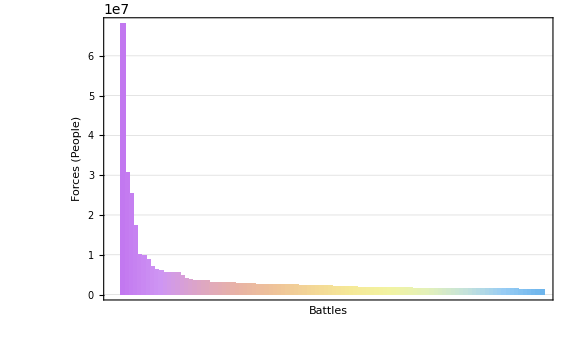

```mathematica
BarChart[
	    largestForcesTips,
	    ChartLabels->Placed[battleNames,"Center"],
	    ChartStyle->"Pastel",
	    AxesLabel->{"Battles","Forces (People)"},
	    LabelStyle->Directive[Bold,Medium],
	    ImageSize->Large,
	    PlotTheme->"Detailed"
	]
```

get the battles with the most number of forces

```mathematica
Total/@ conflictForces[[All, 2]]
```

Part::partd: Part specification <|Operation Green Sea→{Operation Green Sea,{Missing[NotAvailable],Missing[NotAvailable]}},Operation Ivory Coast→{Operation Ivory Coast,{148,12000}},Corrective Movement→{Corrective Movement,{Missing[NotAvailable],Missing[NotAvailable]}},«5»,Operation Gordian Knot→{Operation Gordian Knot,{8000,Missing[NotAvailable]}},Battle of Fire Support Base Ripcord→{Battle of Fire Support Base Ripcord,{Missing[NotAvailable],Missing[NotAvailable]}},«3338»|>⟦All,1,2⟧ is longer than depth of object.

$Aborted

```mathematica
sortedConflicts=SortBy[
		conflictForces,
		Total[DeleteMissing[#]]&
	];
	TakeLargestBy[sortedConflicts,Total[DeleteMissing[#]]&,5]
```

TakeLargestBy::tbnval: Values {1920 Jabal al-Gharbi civil war,1964 Gabon coup d'état,20 July Plot,Action of Arsuf,Baltic Sea Campaigns,Bataan Death March,Battle of Ctesiphon,Chittagong armoury raid,Defence of Festubert,Easter Sunday Raid,«3338»} produced by the function Total[DeleteMissing[#1]]& cannot be used for numerical sorting because they are not all real.

$Aborted

## Geopolitics

Get me the countries with the top 10 GDP